# Chapter 5 – Computations

This notebook contains the numerical computations used in Chapter 5 of the thesis.

## Case with two polynomials

Consider the functions A1 and A2 associated with the polynomials F_1(X,Y)=X-Y and F_2(X,Y)=X+Y and the convex combination Q1. The weight l varies in [0,1].

```mathematica
Clear[A1,A2,Q1,l0,heightBound1]
```

```mathematica
A1[u_]:=Log[8/(1-u)]
A2[u_]:=Log[2/(1+u)]
Q1[u_,l_]:=l A1[u]+(1-l)A2[u]
```

Compute the derivative of Q1 with respect to u and the critical point u0.

```mathematica
D[Q1[u,l],u]
u0=SolveValues[ D[Q1[u,l],u]==0,u][[1]];
```

l/(1-u)-(1-l)/(1+u)

Compute the second derivative of Q1 with respect to u and check that it is positive in (-1,1).

```mathematica
D[Q1[u,l],{u,2}]
```

l/(1-u)^2+(1-l)/(1+u)^2

```mathematica
FullSimplify[D[Q1[u,l],{u,2}]>0,Assumptions->-1<u<1&&0<=l<=1]
```

True

For 0<l<1, the function Q1(u,l) is strictly convex on (-1,1). Hence, its global minimum is attained at the critical point u0. We then maximize Q1(u0,l) with respect to l. 
We differentiate with respect to l and determine the critical point l0.

```mathematica
D[Q1[u0,l],l]
```

-1+(2 (1-l))/(2-2 l)-Log[2/(2-2 l)]+Log[4/l]

```mathematica
l0=SolveValues[D[Q1[u0,l],l]==0,l][[1]]
```

4/5

Check that the second derivative is negative.

```mathematica
D[Q1[u0,l],{l,2}]//Apart
```

1/(-1+l)-1/l

```mathematica
FullSimplify[D[Q1[u0,l],{l,2}]<0,Assumptions->0<l<1]
```

True

Compute sup_(l∈[0,1]) inf_(u∈[-1,1]) Q1[u,l] and the height bound.

```mathematica
Q1[u0/.{l->l0},l0]
```

Log[5]

```mathematica
heightBound1=Q1[u0/.{l->l0},l0]/12
```

Log[5]/12

## Case with three polynomials

Consider the function A_3 associated with the polynomial F_3(X,Y)=5 X^2+6XY+5 Y^2 and the convex combination Q2 of A1, A2, and A3. The weights l_1 and l_2 are nonnegative and such that l_1+l_2≤1.

```mathematica
Clear[A3,Q2,dQ2du,criticalPointRulesQ2,q1,q2,eps,MaximizingF,L1,L2,heightBound2,uLeft,uRight]
```

```mathematica
A3[u_]:=Log[8/Abs[5u + 3]]
Q2[u_,l1_,l2_]:=l1 A1[u]+l2 A2[u]+(1-l1-l2)A3[u]
```

We compute the critical points u1 and u2 of Q2 on the intervals (-1,-3/5) and (-3/5,1).

```mathematica
dQ2du=D[Q2[u,l1,l2],u]//ComplexExpand (*ComplexExpand avoids issues with the derivative of Abs*)
```

l1/(1-u)-l2/(1+u)-5/(3+5 u)+(5 l1)/(3+5 u)+(5 l2)/(3+5 u)

```mathematica
criticalPointRulesQ2=Solve[dQ2du==0,u]
```

{{u→1/5 (-4 l1+l2-√(25-40 l1+16 l1^2-10 l2-8 l1 l2+l2^2))},{u→1/5 (-4 l1+l2+√(25-40 l1+16 l1^2-10 l2-8 l1 l2+l2^2))}}

```mathematica
q1[l1_,l2_]=Q2[u/.criticalPointRulesQ2[[1]],l1,l2];
q2[l1_,l2_]=Q2[u/.criticalPointRulesQ2[[2]],l1,l2];
```

To numerically compute sup_(l_1≥0,l_2≥0,l_1+l_2≤1) min{Q2[u1,l_1,l_2],Q2[u2,l_1,l_2]}, first define the function min{Q2[u1,l_1,l_2],Q2[u2,l_1,l_2]}. The parameter eps is introduced to avoid convergence issues.

```mathematica
eps=10^-16;
```

```mathematica
MaximizingF[l1_?NumericQ,l2_?NumericQ]:=
If[
l1>=eps&&l2>=eps&&l1+l2<=1-eps,
Min[q1[l1,l2],q2[l1,l2]],-1
];
```

Compute the height lower bound and the optimal weights attaining it.

```mathematica
heightBound2=
NMaximize[
{
MaximizingF[l1,l2],
{l1>=eps,l2>=eps,l1+l2<=1-eps}
},
{l1,l2},
MaxIterations->1000,
WorkingPrecision->50,
AccuracyGoal->25
];heightBound2
```

{1.6823461190590914361922170690270219640199633241724,{l1→0.71928667136127294289150824520156509525425350978239,l2→0.14749386462610026647490856386182079201540064811466}}

We consider the truncated values L1=0.719286 and L2=0.147493 and compute the corresponding critical points.

```mathematica
L1=0.719286;
L2=0.147493;
```

```mathematica
uLeft=u/.criticalPointRulesQ2[[1]]/.{l1->L1,l2->L2}
```

-0.84289

```mathematica
uRight=u/.criticalPointRulesQ2[[2]]/.{l1->L1,l2->L2}
```

-0.248971

We have the following lower bound for the height.

```mathematica
1/12 Min[Q2[uLeft,L1,L2],Q2[uRight,L1,L2]]
```

0.140195

## Case with four polynomials

### Finding the fourth polynomial

Consider the polynomial B[u,a,b]=a(u-1)^2+8b(u-1)+64. We compute the real values aReal and bReal for which B[uLeft,aReal,bReal]=B[uRight,aReal,bReal]=0.

```mathematica
Clear[B,L,aReal,bReal,aRounded,bRounded,R,fig]
```

```mathematica
B[u_,a_,b_]:=a(u-1)^2+8b(u-1)+64
```

```mathematica
L=SolveValues[B[uLeft,a,b]==0&&B[uRight,a,b]==0,{a,b}][[1]]
```

{27.8054,10.7463}

```mathematica
aReal=L[[1]]
```

27.8054

```mathematica
bReal=L[[2]]
```

10.7463

Let aRounded and bRounded be the nearest integers to aReal and bReal, respectively. We look for integers a and b such that |B[uLeft,a,b]|≤R and |B[uRight,a,b]|≤R, where R=Max[|B[uLeft,aRounded,bRounded]|,|B[uRight,aRounded,bRounded]|].

```mathematica
aRounded=Round[aReal]
```

28

```mathematica
bRounded=Round[bReal]
```

11

```mathematica
R=Max[
Abs[B[uLeft,aRounded,bRounded]],
Abs[B[uRight,aRounded,bRounded]]
]
```

3.0795

```mathematica
Reduce[Abs[B[uLeft,a,b]]<=R&&Abs[B[uRight,a,b]]<=R,{a,b},Integers]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(a==24&&b==10)||(a==29&&b==11)||(a==34&&b==12)

The feasible region and the relevant integer points are shown below.

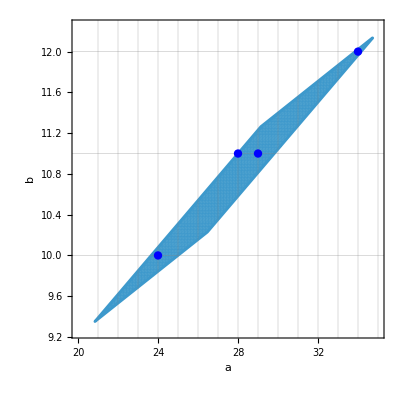

```mathematica
fig=RegionPlot[
Abs[B[uLeft,a,b]]<=R&&Abs[B[uRight,a,b]]<=R,
{a,20,35},
{b,9.25,12.25},

PlotPoints->400,
GridLines->{Range[21,35,1],Range[9,12,1]},
FrameLabel->{a,b},

PlotRange->{{20,35},{9.25,12.25}},
PlotRangeClipping->False,
ImagePadding->30,

Epilog->{
Blue,
PointSize[0.015],
Point[{{24,10},{29,11},{34,12},{28,11}}]
}(*Points are in Epilog to avoid rendering issues when exporting into EPS*)
]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"picture.eps"}],fig,"EPS"];
```

Among the candidate integer pairs, the pair (a,b)=(29,11) minimizes Max[|B[uLeft,a,b]|,|B[uRight,a,b]|].

```mathematica
Max[Abs[B[uLeft,24,10]],Abs[B[uRight,24,10]]]
```

1.92136

```mathematica
Max[Abs[B[uLeft,28,11]],Abs[B[uRight,28,11]]]
```

3.0795

```mathematica
Max[Abs[B[uLeft,29,11]],Abs[B[uRight,29,11]]]
```

0.671514

```mathematica
Max[Abs[B[uLeft,34,12]],Abs[B[uRight,34,12]]]
```

2.86364

### Computing the bound

Consider the polynomial F(X,Y)=29 X^4+60 X^3 Y+78 X^2 Y^2+60 XY^3+29 Y^4 and the associated function A4.

```mathematica
Clear[A4,Q3,dQ3du,poly,heightBound3]
```

```mathematica
A4[u_]:=1/2 Log[64/Abs[29 u^2+30u+5]]
```

Consider the convex combination Q3 of A1,...,A4.

```mathematica
Q3[u_,l1_,l2_,l3_]:=l1 A1[u]+l2 A2[u]+l3 A3[u]+(1-l1-l2-l3)A4[u];Q3[u,l1,l2,l3]
```

l1 Log[8/(1-u)]+l2 Log[2/(1+u)]+l3 Log[8/Abs[3+5 u]]+1/2 (1-l1-l2-l3) Log[64/Abs[5+30 u+29 u^2]]

Compute the first and second derivatives of Q3.

```mathematica
dQ3du=D[Q3[u,l1,l2,l3],u]//ComplexExpand
```

l1/(1-u)-l2/(1+u)-(5 l3)/(3+5 u)-15/(5+30 u+29 u^2)+(15 l1)/(5+30 u+29 u^2)+(15 l2)/(5+30 u+29 u^2)+(15 l3)/(5+30 u+29 u^2)-(29 u)/(5+30 u+29 u^2)+(29 l1 u)/(5+30 u+29 u^2)+(29 l2 u)/(5+30 u+29 u^2)+(29 l3 u)/(5+30 u+29 u^2)

```mathematica
D[Q3[u,l1,l2,l3],{u,2}]//ComplexExpand//FullSimplify
```

l1/(-1+u)^2+l2/(1+u)^2+(25 l3)/(3+5 u)^2-(160 (-1+l1+l2+l3))/(5+u (30+29 u))^2-(29 (-1+l1+l2+l3))/(5+u (30+29 u))

To compute the critical points of Q3, we compute the zeros of the numerator of its derivative. Then, to obtain the height bound, we maximize over l1,l2,l3.

```mathematica
poly=Numerator[Together[dQ3du]];
MaximizingF1[ll1_?NumericQ,ll2_?NumericQ,ll3_?NumericQ]:=(*?NumericQ ensures that the arguments are numeric quantities*)Module[
{roots},
roots=NSolveValues[(poly/. {l1->ll1,l2->ll2,l3->ll3})==0,u∈Reals];(*Numerical search of the real roots of the first derivative*)
If[Length[roots]!=4,Return[-1]];(*Reject evaluation unless 4 roots are found*)
Min[N[Q3[#,ll1,ll2,ll3]&/@roots]]
]
heightBound3=
NMaximize[
{
MaximizingF1[l1,l2,l3],
eps<=l1<=1-eps&&eps<=l2<=1-eps&&eps<=l3<=1-eps&&l1+l2+l3<=1-eps
},
{l1,l2,l3},
MaxIterations->1000,
WorkingPrecision->50,
AccuracyGoal->25
]
```

{1.7019730989901069584391279931878671050071716308594,{l1→0.66568688952589360623031811300503128206085547897646,l2→0.12626310533979010419175492570846054819722251128813,l3→0.11563344218391726264303495339805415133400622780381}}

Numerically, we have the following lower bound for the height.

```mathematica
heightBound3[[1]]/12
```

0.14183109158250891320326066609898892541726430257161

Compute the critical points.

```mathematica
SolveValues[(poly/.heightBound3[[2]])==0,u]
```

{-0.90710250531708323802361563189399635826852449336,-0.75741824252936203974702126065385442090768755786,-0.36343057187187551848344159798419166160090860406,-0.028773487286536299784064410300633378971669378176}